```mathematica
dir=NotebookDirectory[]
```

/home/nicolas/git/spectrum_quasicrystals/hierarchical chain/

```mathematica
(* Thickness *)
th=0.003;
```

## Généralités

```mathematica
(* matrice de transfert d'un site au suivant *)
M[tr_,tl_,e_]:={{e/tr,-tl/tr},{1,0}};
(* matrice de transfert de la 2-molécule *)
M1=M[1,v,e].M[v,1,e];
%//MatrixForm
```

(e^2/v-v | -e/v
e/v | -1/v)

```mathematica
(* matrice de transfert de la 4-molécule *)
M1/.v->r v;
%.M1//Expand;
M2=%
```

{{-e^2/r-e^2 r-e^2/(r v^2)+e^4/(r v^2)+r v^2,e r+e/(r v^2)-e^3/(r v^2)},{-e/r-e/(r v^2)+e^3/(r v^2),1/(r v^2)-e^2/(r v^2)}}

```mathematica
(* couplages renormalisés *)
vv=(r v^2)/(e^2-1);
e1=e(1-r^-1 vv);
e2=e(1-r vv);
(* la 4-molécule correspond bien à une 2-molécule avec les couplages renormalisés *)
M[1,vv,e2].M[vv,1,e1];
%//Expand//Simplify;
%==Simplify[M2]
```

True

## Molécules isolées

#### Intro

```mathematica
(* matrice de transfert de la 2-molécule *)
M1=M[1,v,e].M[v,1,e];
M1//MatrixForm
```

(e^2/v-v | -e/v
e/v | -1/v)

```mathematica
(* hamiltonien dans la base atomique *)
h4={{0,1,0,0},{1,0,v,0},{0,v,0,1},{0,0,1,0}};
%//MatrixForm
```

(0 | 1 | 0 | 0
1 | 0 | v | 0
0 | v | 0 | 1
0 | 0 | 1 | 0)

Dans le cas d’une molécule isolée on a des conditions aux limites nulles. Cela donne pour la fonction d’onde d’énergie E dont les coefficients sont les ψ_i dans la base atomique les conditions :
E ψ_0 = t_(0,1) ψ_1
E ψ_N= t_(N,N-1) ψ_(N-1) 
Dans la suite on suppose t_(0,1)=t_(N,N-1)=1. C’est de toute façon le cas pour nos molécules.
On peut grâce à la condition aux limites au bord gauche choisir (ψ_1, ψ_0) = (E, 1). Le vecteur propre ne sera alors pas normalisé, mais peu importe. 
Appelons M la matrice de transfert qui va d’un bord à l’autre du système, ie celle qui donne :
M (ψ_1, ψ_0) = (ψ_N, ψ_(N-1))
Après application de M sur (ψ_1, ψ_0), on obtient ψ_N comme un polynôme de degré N-1 en E. Grâce à la condition aux limites au bord droit on obtient une équation polynomiale de degré N à résoudre, qui nous donne les N énergies propres du système.

```mathematica
M1.{e ,1}//Expand;
spec4=Solve[e*%[[1]]==%[[2]],e]
(* les énergies obtenues sont bien celles de la 4-molécule *)
Eigenvalues[h4]
```

{{e→1/2 (-v-√(4+v^2))},{e→1/2 (v-√(4+v^2))},{e→1/2 (-v+√(4+v^2))},{e→1/2 (v+√(4+v^2))}}

{1/2 (-v-√(4+v^2)),1/2 (v-√(4+v^2)),1/2 (-v+√(4+v^2)),1/2 (v+√(4+v^2))}

La matrice de transfert nous donne aussi les vecteurs propres.

```mathematica
Block[
{i=4,vp},
vp={1,e ,(M1.{e ,1})[[2]],(M1.{e ,1})[[1]]}/.spec4[[i]];
Print[vp//Expand];
((e/.spec4[[i]])^-1*h4.vp)//FullSimplify//Expand
]
```

{1,v/2+(√(4+v^2))/2,v/2+(√(4+v^2))/2,1}

{1,v/2+(√(4+v^2))/2,v/2+(√(4+v^2))/2,1}

### Renormalization

```mathematica
(* matrice de transfert d'un site au suivant *)
M[tr_,tl_,e_]:={{e/tr,-tl/tr},{1,0}};
```

```mathematica
Clear[vv];
M[r v,1,e].M[1,v,e].M[v,1,e].M[1,r v,e];
%//Expand//Simplify//MatrixForm
(* to be compared with *)
M[vv,1,ee].M[1,vv,ee];
%//Expand//Simplify//MatrixForm
(* check *)
M[vv,1,ee].M[1,vv,ee]/.{ee->e/v(e^2-v^2-1),vv->r(e^2-v^2)};
%//Expand//Simplify//MatrixForm
```

((1+e^4-e^2 (2+v^2))/(r v^2) | (e-e^3+e v^2)/v
(e (-1+e^2-v^2))/v | r (-e^2+v^2))

((-1+ee^2)/vv | -ee
ee | -vv)

((1+e^4-e^2 (2+v^2))/(r v^2) | (e-e^3+e v^2)/v
(e (-1+e^2-v^2))/v | r (-e^2+v^2))

```mathematica
Clear[vv];
M[r v,1,e].M[1,v,e].M[v,1,e].M[1,r^2 v,e];
%//Expand//Simplify//MatrixForm
(* to be compared with *)
M[vv,1,ee].M[1,r vv,ee];
%//Expand//Simplify//MatrixForm
(* check *)
M[ vv,1,ee].M[1,r vv,ee]/.{ee->e/v(e^2-v^2-1),vv->r(e^2-v^2)};
%//Expand//Simplify//MatrixForm
```

((1+e^4-e^2 (2+v^2))/(r v^2) | (e r (1-e^2+v^2))/v
(e (-1+e^2-v^2))/v | r^2 (-e^2+v^2))

((-1+ee^2)/vv | -ee r
ee | -r vv)

((1+e^4-e^2 (2+v^2))/(r v^2) | (e r (1-e^2+v^2))/v
(e (-1+e^2-v^2))/v | r^2 (-e^2+v^2))

### Spectre

#### Avec une matrice de transfert

```mathematica
(* matrice de transfert de la 4-molécule *)
Clear[M];
M[v_]:={{e^2/v-v,-e/v},{e/v,-1/v}};
```

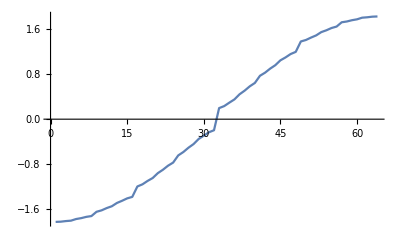

```mathematica
ClearAll[M,vv];
M[vv_]:={{e^2/vv-vv,-e/vv},{e/vv,-1/vv}};
ClearAll[r,v];
Block[{iter=4,v=.9000000000000000000000000000000000000000,r=.900000000000000000000000000000000000000000000000000,mf,transl,spec},
mf=Nest[{Expand[1/2#[[1]].(M[r^(#[[2]]) v]).#[[1]]],#[[2]]+1}&,{1/2 M[v],1},iter][[1]];
transl=mf.{e ,1};
spec=NSolve[e*transl[[1]]==transl[[2]],e,WorkingPrecision->25];
ListPlot[e/.spec,Joined->True]
]
```

#### Diagonalisation directe

```mathematica
(* amplitude de saut entre les sites atomiques i et i+1 *)
Clear[t];
t[i_]:=Block[{k,tt},
k=IntegerExponent[i,2];
If[k==0,tt=1,tt=v r^(k-1)];
tt]
```

```mathematica
(* hamiltonien avec conditions aux bords libres *)
Clear[h];
h[n_]:=Block[{tbl,ar},
tbl=Table[{i,i+1}->t[i],{i,1,2^n-1}];
ar=SparseArray[tbl,{2^n,2^n}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
h[2]//MatrixForm
```

(0 | 1 | 0 | 0
1 | 0 | v | 0
0 | v | 0 | 1
0 | 0 | 1 | 0)

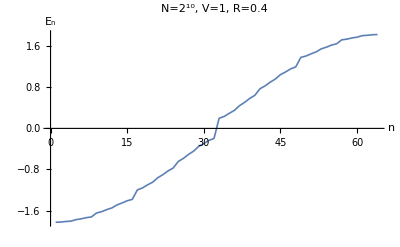

```mathematica
(* spectre *)
Block[{v=.9,r=.9,vp,plot},
vp=Sort[Eigenvalues[h[6]]];
plot=ListPlot[vp,Joined->True,AxesLabel->{"n","E_n"},PlotLabel->"N=2^10, V=1, R=0.4",PlotStyle->Thickness[th]];
(*Export[dir<>"/data/spectrum_isolated_hchain.pdf",plot];*)
Print[plot];
]
```

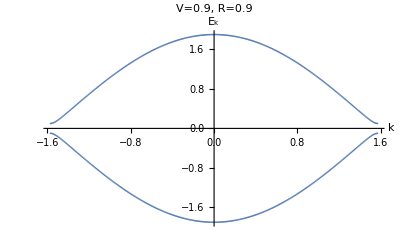

```mathematica
(* spectre de l'approximant périodique de période 2 *)
Block[{v=.9,r=.9,vp,plot,klist,dk=.01,elist},
(* discretized BZ *)
klist=Range[-Pi/2,Pi/2,dk];
(* find the energies associated to each k *)
elist=Flatten[ParallelMap[e/.Solve[(e^2-v^2-1)/v==2 Cos[2#],e]&,klist]];
(* each k corresponds to 2 energies *)
klist=MapThread[{#1,#2}&,{klist,klist}]//Flatten;
plot=ListPlot[MapThread[{#1,#2}&,{klist,elist}],Joined->False,AxesLabel->{"k","E_k"},PlotLabel->"V="<>ToString[v]<>", R="<>ToString[r],PlotStyle->PointSize[.003]];
(*Export[dir<>"/data/spectrum_isolated_hchain.pdf",plot];*)
Print[plot];
]
```

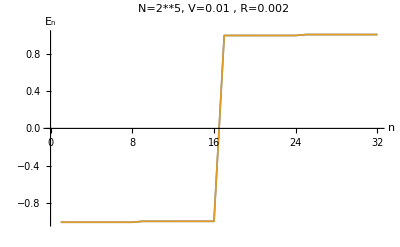

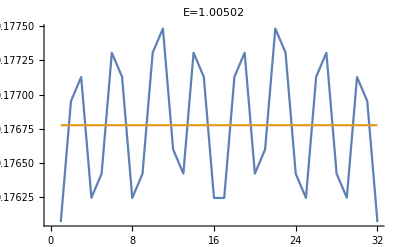

```mathematica
(* spectre, limite V->0,R->0,V<<R, comparaison avec la théorie des perturbations *)
Block[{v=.01,r=.002,vp,plot,i=5,spPerturb,compo,val,vec,vect=2},
vp=Sort[Eigenvalues[h[i]]];
(* components of the energies according to 1st order perturbation theory *)
compo={1}~Join~Table[(r^(it-1)v)/2^it,{it,1,i-1}];
(* spectrum according to 1st order perturbation theory *)
spPerturb=compo.#&/@Tuples[{-1,1},i];
Print[ListPlot[{vp,spPerturb},Joined->True,AxesLabel->{"n","E_n"},PlotLabel->"N=2**"<>ToString[i]<>", V="<>ToString[v]", R="<>ToString[r],PlotStyle->Thickness[th]]];
(*Print[ListPlot[vp-spPerturb]]*)
(* wavefunctions *)
{val,vec}=Eigensystem[h[i]];
Print[ListPlot[{vec[[vect]],Table[1/2^(i/2),{it,2^i}]},Joined->True,PlotLabel->"E="<>ToString@val[[vect]]]];
]
```

```mathematica
(* vecteurs propres *)
Block[{v=1.,r=.3,val,vp,i=8,vect=2,tt,plot},
{val,vp}=Eigensystem[h[i]];
tt=Table[it,{it,2^i}];
plot=ListPlot[vp[[vect]],Joined->True,AxesLabel->{"i","ψ_i"},PlotLabel->"Ground state : E="<>ToString@val[[vect]]<>" \n N=2^8, V=1, R=0.3",Epilog->Point/@ MapThread[{#1,#2}&,{tt,vp[[vect]]}],PlotStyle->Thickness[th]];
Export[dir<>"/data/ground_state_isolated_hchain.pdf",plot];
]
```

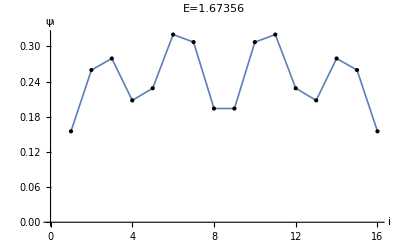

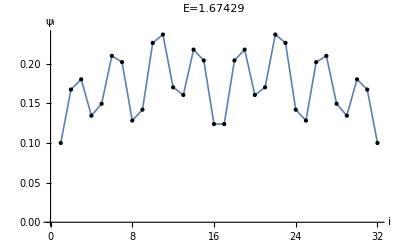

```mathematica
(* vecteurs propres : investigation *)
Block[{v=1.,r=.3,val1,vec1,val2,vec2,i=4,vect=1,tt1,tt2,plot},
{val1,vec1}=Eigensystem[h[i]];
{val2,vec2}=Eigensystem[h[i+1]];
tt1=Table[it,{it,2^i}];
tt2=Table[it,{it,2^(i+1)}];
Print[ListPlot[vec1[[vect]],Joined->True,AxesLabel->{"i","ψ_i"},PlotLabel->"E="<>ToString@val1[[vect]],Epilog->Point/@ MapThread[{#1,#2}&,{tt1,vec1[[vect]]}],PlotStyle->Thickness[th]]];
Print[ListPlot[vec2[[vect]],Joined->True,AxesLabel->{"i","ψ_i"},PlotLabel->"E="<>ToString@val2[[vect]],Epilog->Point/@ MapThread[{#1,#2}&,{tt2,vec2[[vect]]}],PlotStyle->Thickness[th]]];
]
```

#### Dimensions fractales du spectre : fonction de partition

```mathematica
(* hamiltonien avec conditions aux bords périodiques *)
Clear[hp];
hp[n_]:=Block[{tbl,ar},
tbl=Table[{i,i+1}->t[i],{i,1,2^n-1}];
(* clp *)
tbl=Join[tbl,{{1,2^n}->t[2^(n-1)]}];
ar=SparseArray[tbl,{2^n,2^n}];
(* Normal convertit en matrice *)
Normal[ar+Transpose[ar]]
]
hp[2]//MatrixForm
```

(0 | 1 | 0 | v
1 | 0 | v | 0
0 | v | 0 | 1
v | 0 | 1 | 0)

```mathematica
(* hamiltonien avec conditions aux bords antipériodiques *)
Clear[ha];
ha[n_]:=Block[{tbl,ar},
tbl=Table[{i,i+1}->t[i],{i,1,2^n-1}];
(* clp *)
tbl=Join[tbl,{{1,2^n}->-t[2^(n-1)]}];
ar=SparseArray[tbl,{2^n,2^n}];
(* Normal convertit en matrice *)
Normal[ar+Transpose[ar]]
]
ha[2]//MatrixForm
```

(0 | 1 | 0 | -v
1 | 0 | v | 0
0 | v | 0 | 1
-v | 0 | 1 | 0)

```mathematica
(* spectre *)
Block[{v=1.,r=0.3,vpp,vpa,vpn,i=3,plot},
vpp=Sort[Eigenvalues[hp[i]]];
vpa=Sort[Eigenvalues[ha[i]]];
vpn=Sort[Eigenvalues[h[i]]];
(*Print[MapThread[(#1-#2)&,{vpp,vpa}]];*)
plot=ListPlot[{vpp,vpa,vpn},Joined->True,AxesLabel->{"n","E_n"},PlotLabel->"N=2^3, V=1, R=0.4",PlotStyle->Thickness[th],PlotLegends->{"Periodic","Antiperiodic","Free"}];
Export[dir<>"/data/spectra_vs_bc_hchain.pdf",plot];
]
```

```mathematica
Clear[plot]
```

```mathematica
(* calcul des bandes effectives *)
Block[{v=1.,r=.999,vpp,vpa,bandlist,dk,invdos,i=12,plot},
(* spectres des systèmes de taille i p et anti-p *)
vpp=Sort[Eigenvalues[hp[i]]];
vpa=Sort[Eigenvalues[ha[i]]];
invdos = Table[Cos[k],{k,-Pi/2,Pi/2,Pi/(2^i-1)}];
(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bandlist=MapThread[Abs[#1-#2]&,{vpa,vpp}];
dk=N[(2Pi)/2^i];
plot=ListPlot[{bandlist/dk,invdos},Joined->True,AxesLabel->{"n","dE_n/dk"},PlotLabel->"Inverse DoS \n N=2^12, V=1",PlotStyle->Thickness[th],PlotLegends->{"Slightly non-periodic system (R=0.999)","Period 1 system (R=1)"}];
(*Print[plot];*)
Export[dir<>"/data/inverse_dos.pdf",plot];
]
```

les spectres sont calculés !

-0.230845

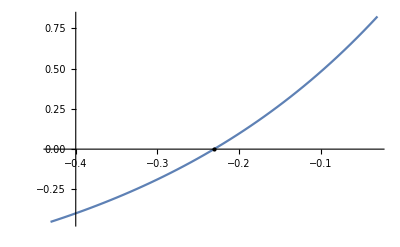

```mathematica
(* dimensions fractales en utilisant les bandes effectives comme largeur de boîte *)
Block[{v=1.,r=.1,vpp,vpa,vppN,vpaN,bandlist,bandlistN,i=11,gam,gamN,τ0},
(* spectres des systèmes de taille i p et anti-p *)
vpp=Sort[Eigenvalues[hp[i]]];
vpa=Sort[Eigenvalues[ha[i]]];
(* spectres des systèmes de taille i+1 p et anti-p *)
vppN=Sort[Eigenvalues[hp[i+1]]];
vpaN=Sort[Eigenvalues[ha[i+1]]];
Print["les spectres sont calculés !"];
(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bandlist=MapThread[Abs[#1-#2]&,{vpa,vpp}];
bandlistN=MapThread[Abs[#1-#2]&,{vpaN,vppN}];
(* limite singulière quand r->1, r<1 !! *)
(*Print[ListPlot[bandlist,Joined->True]];*)
(* calcul des fonctions de partition Subscript[Γ, i] et Subscript[Γ, i+1] *)
gam=2^(-i q)Plus@@((bandlist)^-τ);
gamN=2^(-(i+1) q)Plus@@((bandlistN)^-τ);
(* Subscript[D, 0] *)
τ0=τ/.FindRoot[(gamN/gam/.q->0)-1,{τ,-1}];
Print[τ0];
(* vérif que FindRoot ne s'est pas planté *)
Print[Plot[(gamN/gam/.q->0)-1,{τ,τ0-0.2,τ0+0.2},Epilog->{PointSize[Medium],Point[{τ0,0}]}]]
(*ListPlot[{vpp,vpa},Joined->True]*)
]
```

```mathematica
(* dépendance en la taille du système *)
Clear[d0];
d0[i_,vv_,rr_]:=Block[{v=vv,r=rr,vpp,vpa,vppN,vpaN,bandlist,bandlistN,gam,gamN,τ0},
(* spectres des systèmes de taille i p et anti-p *)
vpp=Sort[Eigenvalues[hp[i]]];
vpa=Sort[Eigenvalues[ha[i]]];
(* spectres des systèmes de taille i+1 p et anti-p *)
vppN=Sort[Eigenvalues[hp[i+1]]];
vpaN=Sort[Eigenvalues[ha[i+1]]];
Print["Système de taille 2^n, n = ", i];
(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bandlist=MapThread[Abs[#1-#2]&,{vpa,vpp}];
bandlistN=MapThread[Abs[#1-#2]&,{vpaN,vppN}];
(* limite singulière quand r->1, r<1 !! *)
(*Print[ListPlot[bandlist,Joined->True]];*)
(* calcul des fonctions de partition Subscript[Γ, i] et Subscript[Γ, i+1] *)
gam=2^(-i q)Plus@@((bandlist)^-τ);
gamN=2^(-(i+1) q)Plus@@((bandlistN)^-τ);
(* Subscript[D, 0] *)
τ0=τ/.FindRoot[(gamN/gam/.q->0)-1,{τ,-1}];
τ0
]
```

```mathematica
d0[5,1.,.1]
```

Système de taille 2^n, n = 5

-0.231305

```mathematica
d0l=Table[d0[i,1.,.3],{i,2,11}]
```

Système de taille 2^n, n = 2

Système de taille 2^n, n = 3

Système de taille 2^n, n = 4

Système de taille 2^n, n = 5

Système de taille 2^n, n = 6

Système de taille 2^n, n = 7

Système de taille 2^n, n = 8

Système de taille 2^n, n = 9

Système de taille 2^n, n = 10

Système de taille 2^n, n = 11

{-0.362884,-0.363461,-0.364026,-0.364084,-0.364086,-0.364086,-0.364086,-0.364086,-0.364086,-0.364086}

```mathematica
Block[{fit,data,plot},
data=MapThread[{#1,#2}&,{Range[1,10],d0l}];
(*Print[ListPlot[data]];*)
fit=LinearModelFit[data[[4;;]],LogN,LogN];
(*Print[Normal[fit]/.LogN->0];*)
plot=Plot[Normal@fit,{LogN,0,11},PlotRange->{{0,11},{-0.362,-0.365}},Epilog->{PointSize@.02,Point@data},AxesLabel->{"Log N","τ(0)"},PlotLabel->"τ(0)=-D_0 \n V=1, R=0.3",PlotStyle->Thickness[th],PlotLegends->Placed[Normal@fit,{Right,Center}]];
Export[dir<>"/data/hausdorff.pdf",plot];
]
```

```mathematica
d0l1=Table[d0[i,1.,1.],{i,2,11}]
```

Système de taille 2^n, n = 2

Système de taille 2^n, n = 3

Système de taille 2^n, n = 4

Système de taille 2^n, n = 5

Système de taille 2^n, n = 6

Système de taille 2^n, n = 7

Système de taille 2^n, n = 8

Système de taille 2^n, n = 9

Système de taille 2^n, n = 10

Système de taille 2^n, n = 11

{-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.}

#### Dimensions fractales du spectre : comptage de boîtes

```mathematica
(* calcule la dimension de Hausdorff d'une liste qui doit être un sous-ensemble ordonné de [0,1] *)
Clear[haus];
haus[list_,n_,δ_]:=Block[{curLbl=1,curBS=0,Δ,b=δ^-n,nboxes=0,len=Length[list],loop},
(* Δ: distance btw the left side of the current box and the current pt *)
Δ=list[[curLbl]]-curBS;
While[curLbl≤len,
loop=False;
(* while the current pt is in the current box, pass to the pt on its right *)
While[Δ≤b&&curLbl<len,curLbl++;Δ=list[[curLbl]]-curBS;loop=True;];
(* after the loop the current box has jumped of Floor[Δ/b] units, and one more box has points in it *)
If[loop,
curBS+=b Floor[Δ/b];nboxes++;Δ=list[[curLbl]]-curBS;,
curLbl++;];
];
Return[nboxes];]
```

```mathematica
(* spectre de la chaîne libre translaté et contracté sur [0,1] *)
Clear[spect];
spect[n_,rr_?NumberQ,vv_?NumberQ]:=Block[{spec,r=rr,v=vv},
spec=Sort[Eigenvalues[h[n]]];
spec=(spec-spec[[1]])/(spec[[-1]]-spec[[1]]);
Return[spec];]
```

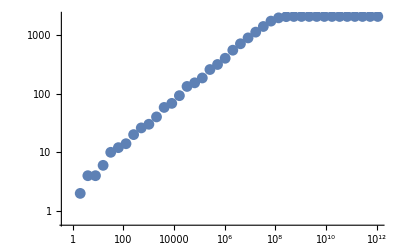

```mathematica
(* plot the number of filled boxes as a function of their (inverse) length, deduce the Hausdorff dimension *)
dat=Module[{v=1.,r=.3,i=11,sp,data,delta=2,nboxes,rg,fit},
sp=spect[i,r,v];
rg=Range[1,40,1];
(* number of filled boxes having length in the range delta^-rg *)
nboxes=ParallelMap[haus[sp,#,delta]&,rg];
(* number of filled boxes as a function of their length *)
data=Parallelize@MapThread[{#1,#2}&,{delta^rg,nboxes}];
Print[ListLogLogPlot[data]];
data
];
```

```mathematica
Block[{plot,fit},
fit=LinearModelFit[Log10@dat[[17;;17+8]],x,x];
plot=Plot[Normal@fit,{x,0,12},Epilog->{PointSize@.02,Point@Log10@dat},AxesLabel->{"Log L^-1","Log N_b"},PlotLabel->"Number of filled boxes N_b \n as a function of their inverse length L, log-log scale. \n N=2^11, V=1, R=0.3",PlotStyle->Thickness[th],PlotLegends->Placed[Normal@fit,{Right,Center}]];
Export[dir<>"/data/box_counting.pdf",plot];
]
```

```mathematica
(* valeur attendue *)
Log[2]/Log[2/r]/.r->.3
```

0.365368

#### Dimensions fractales des fonctions d’ondes : fonction de partition

```mathematica
(* dimensions fractales des fonctions d'onde *)
dWF[q_?NumberQ,i_]:=Block[{v=1.,r=.1,chi,chiN,vec,vecN},
vec=Eigenvectors[h[i]][[2]];
vecN=Eigenvectors[h[i+1]][[2]];
chi=Plus@@((vec)^(2q));
chiN=Plus@@((vecN)^(2q));
(* τ(q) *)
Return[-Log2[chiN/chi]];
]
```

```mathematica
dWF[2,11]
```

0.996794